```mathematica
<<NounouW`
```

HokahokaW`
Git HEAD hash loaded on Mon 6 Apr 2015 17:15:50 is dfc276416b3fda60a30e53692c8c82eaed59709c.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

NounouW`
Git HEAD hash loaded on Mon 6 Apr 2015 19:49:18 is a7b569f93d24f934eedde6a6ac130f15f8bd31fe.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

```mathematica
AllowRaggedArrays[True]
```

## SPP035

```mathematica
layout =JavaNew["nounou.elements.layouts.NNDataLayoutHexagonal", {{-1, 15,14,13,12,11}, {10, 9, 8, 1, 0}, {7, 6, 5, 4}, {-1, 3,2}}]
```

«JavaObject[nounou.elements.layouts.NNDataLayoutHexagonal]»

```mathematica
(layout@mask[#])& /@ {2,4};
```

```mathematica
layout@toJsonString[]
```

{"layoutArray":[[-1,15,14,13,12,11],[10,9,8,1,0],[7,6,5,4],[-1,3,2]],"channelRadius":50.0,"channelDistance":100.0,"masked":[2,4],"className":"nounou.elements.layouts.NNDataLayoutHexagonal","gitHead":"674199eda7404048d811c228fb848bd74709fd6a","version":0.5,"bitmap$0":false}

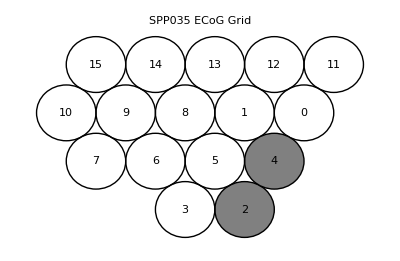

```mathematica
NNDetectorPlot[layout, PlotLabel-> "SPP035 ECoG Grid"]
```

## 16ch sample A

```mathematica
layoutMD16 =JavaNew["nounou.elements.layouts.NNDataLayoutHexagonal", {Prepend[Range[0,4],-1], Range[5,10],  Range[11,15]}]
```

«JavaObject[nounou.elements.layouts.NNDataLayoutHexagonal]»

```mathematica
layoutMD16@toJsonString[]
```

{"layoutArray":[[-1,0,1,2,3,4],[5,6,7,8,9,10],[11,12,13,14,15]],"channelRadius":50.0,"channelDistance":100.0,"masked":[],"className":"nounou.elements.layouts.NNDataLayoutHexagonal","gitHead":"674199eda7404048d811c228fb848bd74709fd6a","version":0.5,"bitmap$0":false}

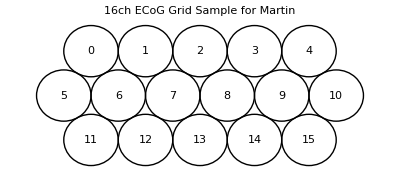

```mathematica
NNDetectorPlot[layoutMD16, PlotLabel-> "16ch ECoG Grid Sample for Martin"]
```

## 16ch sample B

```mathematica
layoutMD16b =JavaNew["nounou.elements.layouts.NNDataLayoutHexagonal", {Prepend[Range[0,3],-1], Range[4,8],  Range[9,12],Range[13,15]}]
```

«JavaObject[nounou.elements.layouts.NNDataLayoutHexagonal]»

```mathematica
layoutMD16b@toJsonString[]
```

{"layoutArray":[[-1,0,1,2,3],[4,5,6,7,8],[9,10,11,12],[13,14,15]],"channelRadius":50.0,"channelDistance":100.0,"masked":[],"className":"nounou.elements.layouts.NNDataLayoutHexagonal","gitHead":"674199eda7404048d811c228fb848bd74709fd6a","version":0.5,"bitmap$0":false}

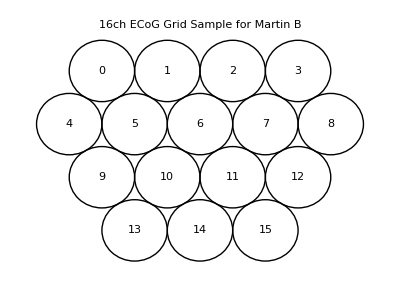

```mathematica
NNDetectorPlot[layoutMD16b, PlotLabel-> "16ch ECoG Grid Sample for Martin B"]
```

## 32ch sample

```mathematica
layoutMD32 =JavaNew["nounou.elements.layouts.NNDataLayoutHexagonal", {Join[{-1,-1},Range[0,5]], Join[{-1},Range[6,12]],Join[{-1},Range[13,18]],  Range[19,25],Range[26,31]}]
```

«JavaObject[nounou.elements.layouts.NNDataLayoutHexagonal]»

```mathematica
layoutMD32@toJsonString[]
```

{"layoutArray":[[-1,-1,0,1,2,3,4,5],[-1,6,7,8,9,10,11,12],[-1,13,14,15,16,17,18],[19,20,21,22,23,24,25],[26,27,28,29,30,31]],"channelRadius":50.0,"channelDistance":100.0,"masked":[],"className":"nounou.elements.layouts.NNDataLayoutHexagonal","gitHead":"674199eda7404048d811c228fb848bd74709fd6a","version":0.5,"bitmap$0":false}

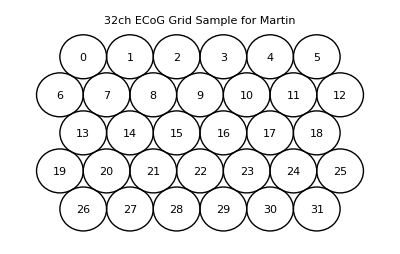

```mathematica
NNDetectorPlot[layoutMD32, PlotLabel-> "32ch ECoG Grid Sample for Martin"]
```